```mathematica
Clear["Global`*"]
$PlotTheme="Scientific";
```

```mathematica
PositivePart[x_]:=If[x>=0,x,0];
c=1;
μ=1;
R = {x, y, z};
$Assumptions = t∈Reals&x ∈ Reals && y ∈ Reals && z ∈ Reals && ρ ∈ Reals && ρ > 0 && θ ∈ Reals && ϕ ∈ Reals && k ∈ Reals && k > 0 && ω > 0&&c∈Reals&&c>0;
r = Sqrt[R . R];
predecessor[α_] := If[α == {0, 0, 0},
   {0, 0, 0},
   Select[
     Table[α - UnitVector[3, j], {j, 1, 3}],
     NonNegative@Min@# &,
     1
     ][[1]]
   ];
firstNonzeroDim[α_] := Position[
     α,
     _?(# > 0 &),
     Infinity, 1
     ][[1]][[1]];
ϵ=1/μ/c^2;
g[α_,f_,direction_] :=If[α == {0, 0, 0},
   1/4/π/r f,
Block[{j, α1, ga},
α1 = α;
j = firstNonzeroDim[α];
α1[[j]] = α1[[j]] - 1;
ga = g[α1,f,direction];
D[ga, R[[j]]] -direction R[[j]]/r D[ga,t]/c // Expand
]
];
h[α_,f_,direction_] :=g[α,f,direction];
SimplifiedHeaviside[x_] := If[x >= 0, 1, 0];
SafeMoment[CurrentMoment_,α_,dim_]:=If[AllTrue[α,#>=0&],
CurrentMoment[α,dim],
0];
ChargeMoment[α_, CurrentMoment_, dim_,direction_] :=-direction  Sum[If[dim == j,
    α[[j]] SimplifiedHeaviside[α[[j]] - 2] (α[[j]] - 1) Integrate[SafeMoment[CurrentMoment,(α[[j]] - 2) UnitVector[3, j] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {j }]], j],t],
    α[[j]] α[[dim]] SimplifiedHeaviside[α[[j]] - 1] SimplifiedHeaviside[α[[dim]] - 1] Integrate[SafeMoment[CurrentMoment,(α[[j]] - 1) UnitVector[3, j] + (α[[dim]] - 1) UnitVector[3, dim] + Total[α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {dim, j}]], j],t]
    ],
   {j, 1, 3}]
ElectricMoment[α_, CurrentMoment_, dim_,direction_] := direction μ D[CurrentMoment[α, dim],t] + 1/ϵ ChargeMoment[α, CurrentMoment, dim,direction]
MagneticMoment[α_,CurrentMoment_, dim_,direction_] := -μ direction Sum[LeviCivitaTensor[3][[dim]][[i]][[j]] SimplifiedHeaviside[α[[i]] - 1] α[[i]] CurrentMoment[(α[[i]] - 1) UnitVector[3, i] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {i}]], j],
   {i, 1, 3}, {j, 1, 3}]
Field[α_, CurrentMoment_, MomentFunction_, dim_,direction_] :=(-1)^Norm[α, 1]/(Times @@ (Factorial/@ α)) h[α,MomentFunction[α, CurrentMoment, dim,direction],direction]
ElectricField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, ElectricMoment, dim,direction];
MagneticField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, MagneticMoment, dim,direction];
On[Assert]
CurrentMoment[α_, dim_] := If[α == {0, 0, 0} && dim == 3, p'[t], 0]
EfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", 
Table[
Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}]ⅇ^(ⅉ k ρ)/.
∫p[t]ⅆt->1/ⅉ/ω p/.
p''[t]->-ω^2 p/.
p'[t]->ⅉ ω p/.
p[t]->p/.
ω->c k;
BfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}]ⅇ^(ⅉ k ρ)/.
∫p[t]ⅆt->1/ⅉ/ω p/.
p''[t]->-ω^2 p/.
p'[t]->ⅉ ω p/.
p[t]->p/.
ω->c k;
P = {0, 0, p};
n = R/r;
HJackson = TransformedField["Cartesian" -> "Spherical",
    c k^2/4/π n×P Exp[ⅉ k r]/r (1 - 1/ⅉ/k/r),
    R -> {ρ, θ, ϕ}] // Simplify;
EJackson = TransformedField["Cartesian" -> "Spherical",
    1/4/π/ϵ Exp[ⅉ k r] (k^2/r (n×P)×n + (3 n (n . P) - P) (1/r^3 - ⅉ k/r^2)),
    R -> {ρ, θ, ϕ}] // Simplify;
Assert[Simplify[BfieldThis - HJackson μ] == {0, 0, 0}]
Assert[Simplify[EfieldThis - EJackson] == {0, 0, 0}]
Clear[CurrentMoment, EfieldThis, BfieldThis, P, n, HJackson, EJackson]
```

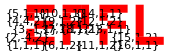

```mathematica
a=4;
length=2a;
(*    1   2   3   4   5   6   7   8   9   10   11   12   13   14   15   16*)
x1s={0,  0, 10,   0,    0, 45, 45, 68, 45,  45,    91,   91, 101,   91, 136, 136};
x2s={0, 10,20,  30,  40,  0, 20, 20, 30, 40,      0,    30,   20,   40,   10,     0};
ws={35, 10,23,  10,  35,10,23, 10, 10,  23,  10,   10,    23,   35,   10,   35};
hs={10, 10,10,  10,  10,20,10 ,30 ,10,  10,  20,   10,    10,    10,   40,    10};
(*           1   2   3   4   5   6   7   8   9   10   11   12   13   14   15   16*)
amplitudes={1,-4,-1,   4,   1,   1,   1,   1,    1,   1,       1,     1,     1,     1,      1,     1};
polarities={1,   2,  1,   2,   1,   2,   1,   2,    2,   1,       2,     2,     1,     1,      2,     1};
d1=a;
(*slice=1;;5;
x1s=x1s[[slice]];
x2s=x2s[[slice]];
ws=ws[[slice]];
hs=hs[[slice]];
amplitudes=amplitudes[[slice]];
polarities=polarities[[slice]];*)
Graphics[Flatten@
MapThread[
{{Red,Rectangle[{#1,#2},{#1+#3,#2+#4}]},
{Black,Text[{#5,#6,#7},{#1,#2}]}
}&
,{x1s,x2s,ws,hs,Range[Length@x1s],amplitudes,polarities}],
ImageSize->Small
]
lengthLogo=171;
d2=a*50/lengthLogo;
IntJ=Function[{x0,σ,m},
1/(m+1)((x0+σ/2)^(m+1)-(x0-σ/2)^(m+1))
];
CJ=Function[{α,x1,x2,w,h},
IntJ[x1+w/2,w,α[[1]]]IntJ[x2+h/2,h,α[[2]]]
];
CurrentMoment=If[#1[[3]]==0,
Exp[-t^2] Sum[
If[polarities[[i]]==#2,
CJ[#1,x1s[[i]]/lengthLogo length-d1,x2s[[i]]/lengthLogo length-d2,ws[[i]]/lengthLogo length,hs[[i]]/lengthLogo length]amplitudes[[i]],
0],
{i,1,Length@x1s}],
0]&;
dirName=ToString@NotebookDirectory[];
```

```mathematica
ParallelTable[Block[{Efield,norm,plotLimit,nPoints,xd,yd,normd},
Efield=#1+#2&@@Table[
Table[
Sum[
ElectricField[{ax,ay,0},CurrentMoment,dim,direction]/.t->0-direction r/.z->0,
{ax,0,maxOrder},{ay,0,maxOrder-ax}],
{dim,1,2}],
{direction,-1,1,2}
];
norm=Total[Efield^2];
plotLimit=6/5a;
nPoints=15;
xd=Subdivide[-plotLimit,plotLimit,nPoints];
yd=Subdivide[-plotLimit,plotLimit,nPoints];
normd=norm/.x->xd/.y->yd;
Export[dirName<>"/data/order-"<>ToString[maxOrder]<>".mx",
<|"field"->Efield,"norm"->norm,"x"->xd,"y"->yd,"discrete norm"->normd|>];
ListContourPlot[Transpose@normd,
PlotRange->Full,PlotLabel->maxOrder]
],
{maxOrder,1,10,2}
]
```

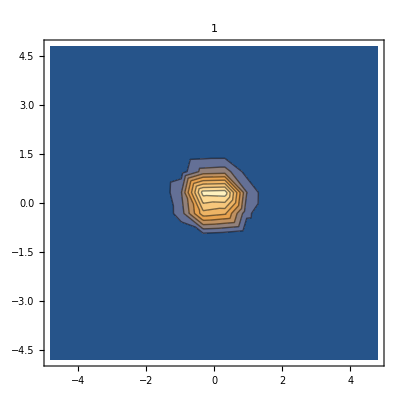
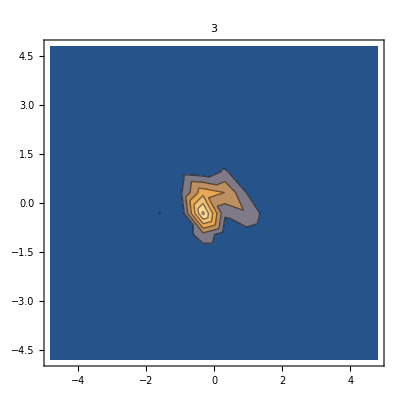
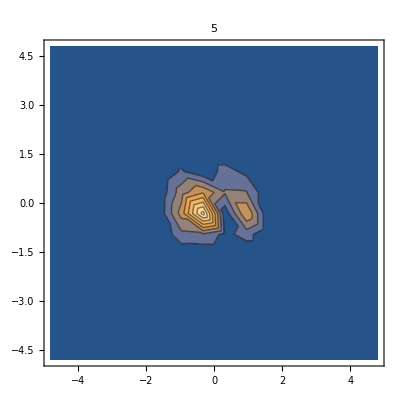
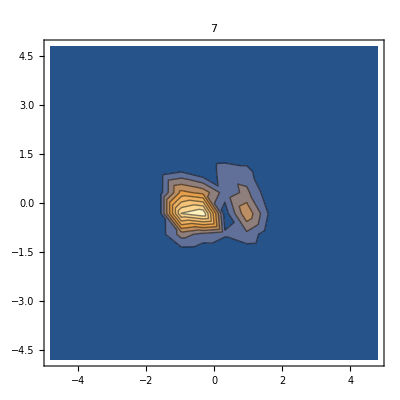
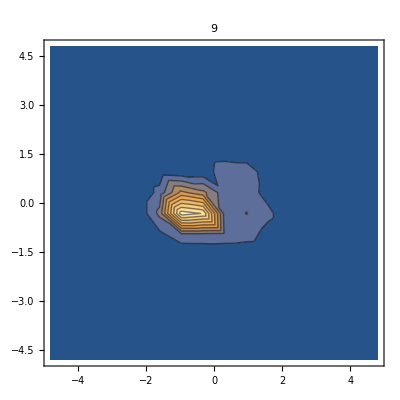
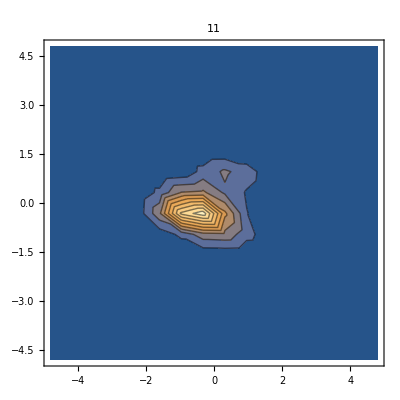
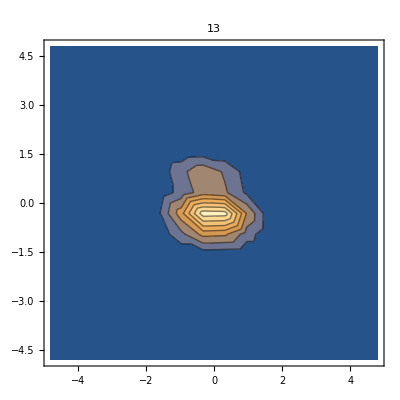
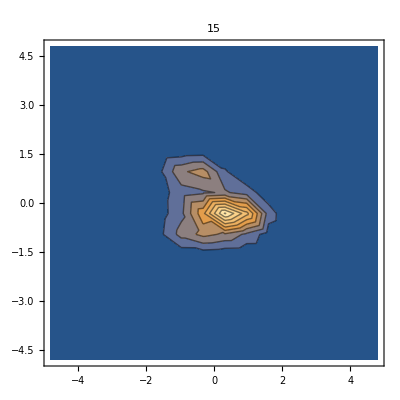

{{{-24/5,-24/5,(-2344783764049308265787774003189/(5208992736159349747125000 ⅇ^(1152/25) π)+23+1/3 (-140688351008963659019/1+1))^2+(1)^2},{-24/5,-24/5,(1)^2+(1)^2},12,{-24/5,-24/5,(1)^2+(1)^2},{-24/5,-24/5,(25+1/60 1)^2+(1)^2}},{1},12,{1},{1}}
 |  |  |  |

{{-24/5,-24/5,(-2344783764049308265787774003189/(5208992736159349747125000 ⅇ^(1152/25) π)+23+1/3 (-140688351008963659019/1+1/1))^2+(241750760657939997450391967/(35004431186990830300680 1 π)+23+1)^2},{-24/5,-24/5,(1)^2+((11)^2},252,{1},{24/5,24/5,(1)^2+(1)^2}}
 |  |  |  |

```mathematica
Table[
imported=Import[dirName<>"/data/order-"<>ToString[order]<>".mx"];
x=imported["x"];
y=imported["y"];
z=imported["discrete norm"];
ListContourPlot[
Flatten[
Table[
{x[[i]],y[[j]],z[[i,j]]},
{i,1,Length@x},{j,1,Length@y}],1],
PlotRange->Full,
PlotLabel->order
],
{order,1,39,2}
]
```

```mathematica
Flatten[
Table[
{N@x[[i]],N@y[[j]],N@z[[i,j]]},
{i,1,Length@x},{j,1,Length@y}],1]
```

{{-4.8,-4.8,6.14778×10^-6},{-4.8,-4.16,0.0000106073},{-4.8,-3.52,0.0000284037},{-4.8,-2.88,0.000100036},{-4.8,-2.24,0.000353447},{-4.8,-1.6,0.00107098},{-4.8,-0.96,0.00245228},{-4.8,-0.32,0.00377734},{-4.8,0.32,0.0036518},{-4.8,0.96,0.0022554},{-4.8,1.6,0.000991541},{-4.8,2.24,0.000364243},{-4.8,2.88,0.000129846},{-4.8,3.52,0.000049197},{-4.8,4.16,0.0000207506},{-4.8,4.8,9.95342×10^-6},{-4.16,-4.8,4.68563×10^-6},{-4.16,-4.16,4.91786×10^-6},{-4.16,-3.52,0.0000202973},{-4.16,-2.88,0.000140095},{-4.16,-2.24,0.000764634},{-4.16,-1.6,0.00330701},{-4.16,-0.96,0.0113273},{-4.16,-0.32,0.0238546},{-4.16,0.32,0.0219239},{-4.16,0.96,0.00941753},{-4.16,1.6,0.0029645},{-4.16,2.24,0.00087803},{-4.16,2.88,0.000257766},{-4.16,3.52,0.0000804082},{-4.16,4.16,0.0000287975},{-4.16,4.8,0.0000125852},{-3.52,-4.8,5.11239×10^-6},{-3.52,-4.16,6.01138×10^-7},{-3.52,-3.52,0.0000190231},{-3.52,-2.88,0.000296588},{-3.52,-2.24,0.00119665},{-3.52,-1.6,0.00311238},{-3.52,-0.96,0.166479},{-3.52,-0.32,0.654011},{-3.52,0.32,0.478061},{-3.52,0.96,0.0623415},{-3.52,1.6,0.000384526},{-3.52,2.24,0.0021377},{-3.52,2.88,0.000626278},{-3.52,3.52,0.000140094},{-3.52,4.16,0.0000376739},{-3.52,4.8,0.0000146903},{-2.88,-4.8,0.0000145966},{-2.88,-4.16,0.0000220178},{-2.88,-3.52,0.000129366},{-2.88,-2.88,0.00184832},{-2.88,-2.24,0.0333024},{-2.88,-1.6,1.27746},{-2.88,-0.96,12.6837},{-2.88,-0.32,18.0705},{-2.88,0.32,13.8117},{-2.88,0.96,9.35734},{-2.88,1.6,1.0057},{-2.88,2.24,0.0327354},{-2.88,2.88,0.00203741},{-2.88,3.52,0.000216904},{-2.88,4.16,0.0000368765},{-2.88,4.8,0.0000142322},{-2.24,-4.8,0.0000426755},{-2.24,-4.16,0.000130798},{-2.24,-3.52,0.000738828},{-2.24,-2.88,0.0123126},{-2.24,-2.24,0.288152},{-2.24,-1.6,1.87734},{-2.24,-0.96,21.1508},{-2.24,-0.32,187.561},{-2.24,0.32,104.48},{-2.24,0.96,6.40855},{-2.24,1.6,4.35008},{-2.24,2.24,0.283043},{-2.24,2.88,0.00690144},{-2.24,3.52,0.000199726},{-2.24,4.16,0.0000134389},{-2.24,4.8,0.0000115106},{-1.6,-4.8,0.0000828473},{-1.6,-4.16,0.00037575},{-1.6,-3.52,0.00281992},{-1.6,-2.88,0.0370287},{-1.6,-2.24,1.23528},{-1.6,-1.6,100.439},{-1.6,-0.96,1142.15},{-1.6,-0.32,1182.85},{-1.6,0.32,1141.29},{-1.6,0.96,1053.12},{-1.6,1.6,95.1196},{-1.6,2.24,1.51167},{-1.6,2.88,0.0178939},{-1.6,3.52,0.000246653},{-1.6,4.16,7.65664×10^-6},{-1.6,4.8,0.0000162606},{-0.96,-4.8,0.000092923},{-0.96,-4.16,0.000527955},{-0.96,-3.52,0.00539216},{-0.96,-2.88,0.0632724},{-0.96,-2.24,0.117134},{-0.96,-1.6,216.053},{-0.96,-0.96,6020.09},{-0.96,-0.32,20112.5},{-0.96,0.32,10792.1},{-0.96,0.96,2379.51},{-0.96,1.6,185.142},{-0.96,2.24,2.11462},{-0.96,2.88,0.0206444},{-0.96,3.52,0.000959756},{-0.96,4.16,0.000110065},{-0.96,4.8,0.0000417188},{-0.32,-4.8,0.0000510203},{-0.32,-4.16,0.000335075},{-0.32,-3.52,0.00485703},{-0.32,-2.88,0.0848305},{-0.32,-2.24,1.20828},{-0.32,-1.6,85.3713},{-0.32,-0.96,4167.51},{-0.32,-0.32,22240.8},{-0.32,0.32,9128.46},{-0.32,0.96,2.7867},{-0.32,1.6,58.5016},{-0.32,2.24,0.70786},{-0.32,2.88,0.0275122},{-0.32,3.52,0.00233412},{-0.32,4.16,0.00029815},{-0.32,4.8,0.0000792004},{0.32,-4.8,7.29718×10^-6},{0.32,-4.16,0.000118505},{0.32,-3.52,0.00369902},{0.32,-2.88,0.0631596},{0.32,-2.24,0.484462},{0.32,-1.6,208.026},{0.32,-0.96,2826.28},{0.32,-0.32,1160.49},{0.32,0.32,3641.21},{0.32,0.96,4045.94},{0.32,1.6,294.558},{0.32,2.24,1.82856},{0.32,2.88,0.0118297},{0.32,3.52,0.00210006},{0.32,4.16,0.000326956},{0.32,4.8,0.0000932667},{0.96,-4.8,5.12931×10^-6},{0.96,-4.16,0.0000941724},{0.96,-3.52,0.00242099},{0.96,-2.88,0.0416523},{0.96,-2.24,2.49303},{0.96,-1.6,264.24},{0.96,-0.96,4307.45},{0.96,-0.32,9531.1},{0.96,0.32,5656.7},{0.96,0.96,3375.21},{0.96,1.6,280.207},{0.96,2.24,2.11762},{0.96,2.88,0.00523937},{0.96,3.52,0.000513098},{0.96,4.16,0.000164834},{0.96,4.8,0.0000754598},{1.6,-4.8,0.0000310112},{1.6,-4.16,0.000202492},{1.6,-3.52,0.00229272},{1.6,-2.88,0.0414136},{1.6,-2.24,1.47272},{1.6,-1.6,64.8829},{1.6,-0.96,962.386},{1.6,-0.32,2406.8},{1.6,0.32,833.012},{1.6,0.96,199.593},{1.6,1.6,28.658},{1.6,2.24,0.51604},{1.6,2.88,0.0019492},{1.6,3.52,0.0000206473},{1.6,4.16,0.0000801567},{1.6,4.8,0.0000575012},{2.24,-4.8,0.0000447887},{2.24,-4.16,0.000205405},{2.24,-3.52,0.00124253},{2.24,-2.88,0.00659117},{2.24,-2.24,0.0233227},{2.24,-1.6,2.11698},{2.24,-0.96,16.9092},{2.24,-0.32,5.79068},{2.24,0.32,18.3675},{2.24,0.96,17.4566},{2.24,1.6,0.626431},{2.24,2.24,0.00609011},{2.24,2.88,0.00195146},{2.24,3.52,0.00024545},{2.24,4.16,0.0000946163},{2.24,4.8,0.000052812},{2.88,-4.8,0.0000378896},{2.88,-4.16,0.000127672},{2.88,-3.52,0.000496221},{2.88,-2.88,0.00187047},{2.88,-2.24,0.0191641},{2.88,-1.6,0.790168},{2.88,-0.96,6.97567},{2.88,-0.32,9.93164},{2.88,0.32,4.33377},{2.88,0.96,2.76026},{2.88,1.6,0.400222},{2.88,2.24,0.0186},{2.88,2.88,0.00151294},{2.88,3.52,0.000309206},{2.88,4.16,0.000107709},{2.88,4.8,0.0000509519},{3.52,-4.8,0.0000255363},{3.52,-4.16,0.0000680276},{3.52,-3.52,0.000203674},{3.52,-2.88,0.000708206},{3.52,-2.24,0.00343582},{3.52,-1.6,0.0249859},{3.52,-0.96,0.103061},{3.52,-0.32,0.0974447},{3.52,0.32,0.0613422},{3.52,0.96,0.0408294},{3.52,1.6,0.00692418},{3.52,2.24,0.00184157},{3.52,2.88,0.000631622},{3.52,3.52,0.000224854},{3.52,4.16,0.0000924215},{3.52,4.8,0.000044588},{4.16,-4.8,0.0000162729},{4.16,-4.16,0.0000373575},{4.16,-3.52,0.0000954963},{4.16,-2.88,0.000272093},{4.16,-2.24,0.000801455},{4.16,-1.6,0.00203441},{4.16,-0.96,0.00343407},{4.16,-0.32,0.00303837},{4.16,0.32,0.00169174},{4.16,0.96,0.00106919},{4.16,1.6,0.000848678},{4.16,2.24,0.00054978},{4.16,2.88,0.000284662},{4.16,3.52,0.000135948},{4.16,4.16,0.0000666024},{4.16,4.8,0.0000350156},{4.8,-4.8,0.0000105433},{4.8,-4.16,0.0000218741},{4.8,-3.52,0.0000490765},{4.8,-2.88,0.000115339},{4.8,-2.24,0.000259753},{4.8,-1.6,0.000491084},{4.8,-0.96,0.000691615},{4.8,-0.32,0.000696664},{4.8,0.32,0.000555196},{4.8,0.96,0.000422768},{4.8,1.6,0.000320948},{4.8,2.24,0.000221993},{4.8,2.88,0.000136498},{4.8,3.52,0.0000781793},{4.8,4.16,0.0000441664},{4.8,4.8,0.0000255317}}